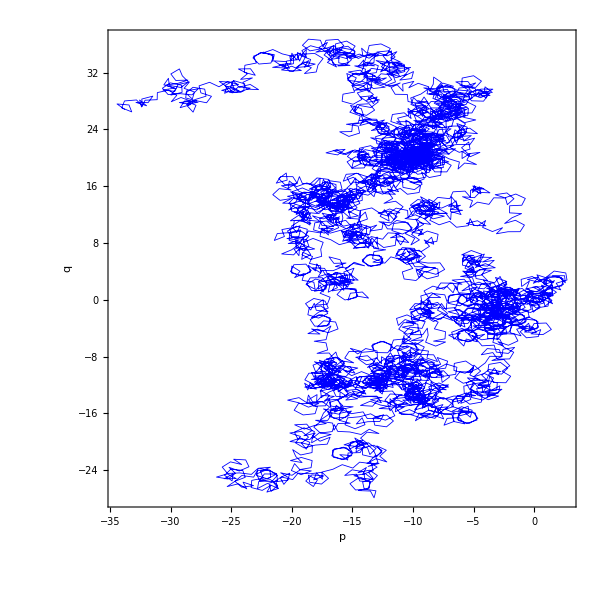

0.997844

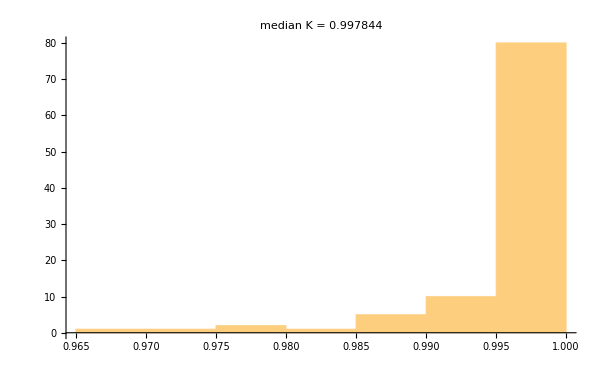

```mathematica
(*----1. input----*)
SeedRandom[42];
len=10000;
x=N@RandomInteger[{0,1},len];        (*swap in your own series*)

(*----2. p-q trajectory----*)
pqPath[v_List,c_]:=Transpose[{Re[#],Im[#]}&@Accumulate[v Exp[I c Range[Length[v]]]]]

c=1.2;

ListLinePlot[pqPath[x,c],PlotStyle->{Blue,Thickness[0.001]},AspectRatio->1,Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["p",Italic,14],Style["q",Italic,14]},ImageSize->600,PlotRangePadding->Scaled[0.05]]

(*----3. K----*)
K01[v_List,cc_]:=Module[{n,z,phiMean,nMax,M,Dc,nn},n=Length[v];
z=Accumulate[v Exp[I cc Range[n]]];
phiMean=Mean[v];
nMax=Floor[n/10];
nn=Range[nMax];
M=Table[Mean[Abs[Drop[z,k]-Drop[z,-k]]^2],{k,1,nMax}];
Dc=M-phiMean^2 (1-Cos[nn cc])/(1-Cos[cc]);
Correlation[N[nn],Dc]]

cs=RandomReal[{Pi/5,4 Pi/5},100];
Ks=K01[x,#]&/@cs;
kStat=Median[Ks]

Histogram[Ks,Automatic,PlotLabel->Row[{"median K = ",kStat}]]
```